# Report Project X

Course code: IX1500
Date: 2022-09-xx

Deni Person, denip@kth.se
William Eriksson, werik@kth.se

Task 1: Texas Hold ‘em Probabilities

## Summary

### Task

In Texas Hold ‘em poker (7 cards), there are a set number of hands - each ranking either higher or lower than the other based on the probability of their existence.
The hands are, ranked high-to-low in order of occurrence:
	* Pair
	* Two pairs
	* No pair/high card
	* Three of a kind
	* Straight
	* Flush
	* Full house
	* Four of a kind
	* Straight Flush
	* Royal Straight Flush
	
(task 1.a). Determine the probability of each hand after a player’s hole cards have been dealt.
(task 1.b). Determine the probability of each hand after a player’s hole cards have been dealt plus 3 of the 5 community cards.

### Result

```mathematica
ClearAll["`*"]
```

## Road Construction

### Model for cross section area

The total number of different 7 cards sets from a standard poker deck where order does not matter is

a(h)=(10+2h)h

The data is interpolated as a function A(x).

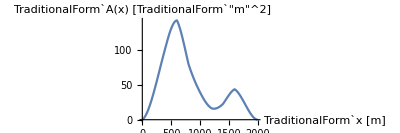

### Model for volume

The requested volume to be transported can be calculated numerically with the integral

V=∫_0^2000 A(x)dx

V≈101×10^3 m^3

I.e. about 0.1 km^3 must be transported.

## Mathematica Data

```mathematica
ClearAll["`*"]
```

```mathematica
data = {{ , 2KnownCards, 5KnownCards},{OnePair, 0.7767146821725915, 0.5855689176688251}, {TwoPairs, 0.2533897185146029, 0.08325624421831637}, {ThreeOfAKind, 0.0683569635069569, 0.013876040703052728}, 
{Straight, 0.02688364892673073, 0.1517113783533765}, {Flush, 0.01971813702354207, 0}, {FullHouse, 0.022329098151749136, 0}, {FourOfAKind, 0.0012592270950933565, 0}, 
{StraightFlush, 0.0008316184938360173, 0},
{RoyalStraightFlush, 0.00000320942438029791, 0}}
```

{{Null,2 KnownCards,5 KnownCards},{OnePair,0.776715,0.585569},{TwoPairs,0.25339,0.0832562},{ThreeOfAKind,0.068357,0.013876},{Straight,0.0268836,0.151711},{Flush,0.0197181,0},{FullHouse,0.0223291,0},{FourOfAKind,0.00125923,0},{StraightFlush,0.000831618,0},{RoyalStraightFlush,3.20942×10^-6,0}}

```mathematica
ass= Grid[data,Alignment->Left,Spacings->{2,1},Frame->All,ItemStyle->"Text",Background->{{Gray,None},{LightGray,None}}]
```

| 2 KnownCards | 5 KnownCards
OnePair | 0.776715 | 0.585569
TwoPairs | 0.25339 | 0.0832562
ThreeOfAKind | 0.068357 | 0.013876
Straight | 0.0268836 | 0.151711
Flush | 0.0197181 | 0
FullHouse | 0.0223291 | 0
FourOfAKind | 0.00125923 | 0
StraightFlush | 0.000831618 | 0
RoyalStraightFlush | 3.20942×10^-6 | 0

## Code

```mathematica
import math
import random
from itertools import combinations
from operator import attrgetter

""" 

* one pair
* two pairs
* three of a kind
* straight
* flush
* full house 
* four of a kinddqdq
* straight flush
* straight royal flush

"""

class Card:

    color = ""
    number = 0

    def __init__(self, c, n):
        self.color = c
        self.number = n
    
    def __repr__(self):
        return f"{self.color}, {self.number}"


def main():
    deck = generate_deck()
    hand = pull_cards_from_deck(deck, 2)
    print("First round:")
    test_hand = [Card("Ass", 2), Card("Ass", 1), Card("Ass", 2), Card("Ass", 1)]
    calculate_prob(hand, deck, 5)
    hand += pull_cards_from_deck(deck, 3)
    print("Second round:")
    calculate_prob(hand, deck, 2)

def print_cards(cards, description):

    print(description)

    for c in range(len(cards)):
        print(cards[c].color, cards[c].number, end=" ")

    print("\n")

def calculate_prob(hand, deck, community_card_count):

    print(hand)
    unknowns = combinations(deck, community_card_count)

    tuples = []

    for j in combinations(deck, community_card_count):
        tuples.append(unknowns.__next__())

    found_pairs = 0
    found_two_pair = 0
    found_three_of = 0
    found_royal_flushes = 0
    found_flushes = 0
    found_straight_flushes = 0
    found_straight = 0
    found_full_house = 0
    found_four_of_a_kind = 0

    for i in range(len(tuples)):
        combo = []
        for j in range(community_card_count):
            combo.append(tuples[i][j])

        found_pairs += one_pair(combo+hand)
        found_two_pair += two_pairs(combo+hand)
        found_three_of += three_of_a_kind(combo+hand)
        found_royal_flushes += royal_straight_flush(combo+hand)
        found_straight += check_straight(combo+hand)
        found_flushes += check_flush(combo+hand)
        found_straight_flushes += check_straight_flush(combo+hand)
        found_full_house += full_house(combo+hand)
        found_four_of_a_kind += four_of_a_kind(combo+hand)

    
    print("Probabilities:")
    print("")
    print("One pair: ", found_pairs/len(tuples))
    print("Two pairs: ", found_two_pair/len(tuples))
    print("Three of a kind: ", found_three_of/len(tuples))
    print("Straight: ", found_straight/len(tuples))
    print("Flush: ", found_flushes/len(tuples))
    print("Full house: ", found_full_house/len(tuples))
    print("Four of a kind: ", found_four_of_a_kind/len(tuples))
    print("Straight flush: ", found_straight_flushes/len(tuples))
    print("Royal straight flush: ", found_royal_flushes/len(tuples))
    print("")


def one_pair(combination) -> int:
    for i in range(len(combination)):    
        for j in range(i+1,len(combination)):
            if j >= len(combination):
                break
            if combination[i].number == combination[j].number:
                #print(f"{combination[i].number} | {combination[j].number}")
                return 1
    return 0


def two_pairs(combination) -> int:
    found_pairs = 0
    
    for i in range(len(combination)):    
        for j in range(i+1,len(combination)):
            if j >= len(combination):
                break
            if combination[i].number == combination[j].number:
                combination.remove(combination[i])
                combination.remove(combination[j-1])
                found_pairs+= 1

    for i in range(len(combination)):    
        for j in range(i+1,len(combination)):
            if j >= len(combination):
                break
            if combination[i].number == combination[j].number:
                found_pairs+= 1
                break

    if found_pairs >= 2:
        return 1

    return 0


            
def three_of_a_kind(combinations):
    combinations.sort(key= attrgetter('number'))

    found = 0

    for i in range(len(combinations)):

        cards = 1
        for j in range(i+1, len(combinations)):

            if combinations[j].number != combinations[i].number:
                break
            else:
                cards += 1

            if(cards >= 3):
                found = 1
                break

    return found 

           
def four_of_a_kind(combinations):
    combinations.sort(key= attrgetter('number'))

    found = 0

    for i in range(len(combinations)):

        cards = 1
        for j in range(i+1, len(combinations)):

            if combinations[j].number != combinations[i].number:
                break
            else:
                cards += 1

            if(cards >= 4):
                found = 1
                break

    return found 


def full_house(combinations):
    combinations.sort(key= attrgetter('number'))

    found = 0

    for i in range(len(combinations)):

        cards = 1
        for j in range(i+1, len(combinations)):

            if combinations[j].number != combinations[i].number:
                break
            else:
                cards += 1

            if(cards >= 3):
                found = 1
                combinations.remove(combinations[j])
                combinations.remove(combinations[j-1])
                combinations.remove(combinations[j-2])
                break


    if(found == 1):
        found = one_pair(combinations)

    return found 


def check_flush(combinations):

    flush = 0

    for i in range(len(combinations)):
        same_suit = 1
        for j in range(i+1, len(combinations)):
            if(combinations[i].color == combinations[j].color):
                same_suit += 1
            
            if(same_suit >= 5):
                flush = 1
                break   

    return flush

def check_straight(combinations):
    combinations.sort(key= attrgetter('number'))

    found = 0

    for i in range(len(combinations)):
        straight = 1
        for j in range(i+1, len(combinations)):

            if combinations[j].number != combinations[i].number + j - i:
                break
            else:
                straight += 1
                if(combinations[j].number == 13 and straight == 4):
                    if(combinations[0].number == 1):
                        found = 1
                        break

            if(straight >= 5):
                found = 1
                break

    return found

def check_straight_flush(combinations):
    if(check_straight(combinations) == 1 and check_flush(combinations)== 1):
        return 1
    else:
        return 0

def royal_straight_flush(combinations):
    king_exists = False
    s_exists = False

    for i in range(len(combinations)):
        if(combinations[i].number == 1):
            s_exists = True
        if(combinations[i].number == 13):
            king_exists = True
    
    if(king_exists and s_exists and check_straight_flush(combinations) == 1):
        return 1
    
    return 0




def generate_deck():
    colors = ["hjärter", "spader", "ruter", "klöver"]
    numbers = [1, 2, 3, 4, 5, 6, 7, 8, 9, 10, 11, 12, 13]
    cards = []
    for j in numbers:
        for i in colors:
            new_card = Card(i, j)
            cards.append(new_card)

    return cards

def pull_cards_from_deck(deck, cards_to_draw):
    
    pulled_cards = []

    for i in range(cards_to_draw):
        card = deck[random.randint(0, len(deck)-1)]
        deck.remove(card)
        pulled_cards.append(card)

    return pulled_cards

        

main()
```

Task 2: Kick Length

## Summary

### Task

A certain football path can be described by the following differential equations.

{m x''(t)=-μ x'(t) Abs[x'(t)]
m y''(t)=-m g-μ y'(t)Abs[y'(t)]

In this case, the friction force is proportional to the square of the speed v^2 and opposite to the velocity v⃗. Determine the kick angle toward the ground which gives the greatest kick length. Assume the following data:

m=0.4kg, μ=0.01 kg/m, g=9.8m/s^2

### Result

The differential equations are solved numerically for different angles and then a function L(θ) is interpolated whose maximum is determined.

L_max≈35m, θ_max≈42°

## Kick Length

### Solution to the differential equations

The angle θ is set which gives initial values (x(0),y(0))=(0,0) och (x'(0),y'(0))=v_0(cos(θ),sin(θ)). Thereafter, the differential equations are solved numerically.

{m x''(t)=-μ x'(t)√((x'(t))^2)
m y''(t)=-m g-μ y'(t)√((y'(t))^2)

The kick time t_0 is determined so that y(t_0)=0. Finally, the kick length is L=x(t_0).

The above procedure is repeated for different angles and then interpolated a function L(θ) whose maximum is determined.

L_max≈35m, θ_max≈42°

### Calculation of kick time and kick length

The time t_0 is determined so that y(t_0)=0. Finally the kick length is computed as L=x(t_0).

The solution is repeated for different angles and then interpolated a function L(θ) whose maximum is determined.

θ | 10 | 20 | 30 | 40 | 50 | 60 | 70 | 80
L | 17.2434 | 27.3526 | 32.7388 | 34.6327 | 33.6694 | 30.0809 | 23.7545 | 14.1591

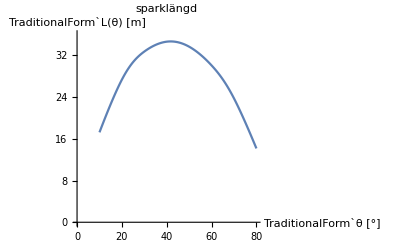

The maximum is computed as

L_max≈35m, θ_max≈41°

## Code

```mathematica
ClearAll["`*"]
```

Enter given data.

```mathematica
m=0.4;μ=0.01;g=9.8;v0=25;
```

Define differential equations and there initial conditions.

```mathematica
de[θ_]:={
m x''[t]==-μ x'[t] √(x'[t]^2),
m y''[t]==-m g-μ y'[t] √(y'[t]^2),
x[0]==0,y[0]==0,x'[0]==v0 Cos[θ],y'[0]==v0 Sin[θ]
}
```

Solve the DE.

```mathematica
sol[θ_]:=NDSolve[de[θ],{x,y},{t,0,5}]
```

Example for θ=45°

```mathematica
sol[45°]
```

```mathematica
ParametricPlot[
Evaluate[{x[t],y[t]}/.sol[45°]],{t,0,3.5},
AxesLabel->{"x","y"},PlotRange->{{0,40},{-5,15}}
]
```

The curve for different angles.

```mathematica
Manipulate[
ParametricPlot[
Evaluate[{x[t],y[t]}/.sol[θ]],{t,0,3.5},
AxesLabel->{"x","y"},
PlotLabel->StringForm["θ = `1`°",θ/Degree],
PlotRange->{{0,40},{-5,15}}
],
{{θ,45°},25°,55°}
]
```

The function for kick length.

```mathematica
len[θ_]:=Module[
{t0},
t0=t/.FindRoot[Evaluate[y[t]/.sol[θ]]==0,{t,2,4}];
First[x[t0]/.sol[θ]]
]
```

Example

```mathematica
len[45°]
```

A table for different angles.

```mathematica
data=Table[{θ,len[θ °]},{θ,10,80,10}]
```

```mathematica
TableForm[Transpose[data],TableHeadings->{{θ,L},None}]
```

```mathematica
ListLinePlot[data,InterpolationOrder->3,PlotRange->{0,36},AxesLabel->{StringForm["`1` [°]",θ],StringForm["`1` [m]",L[θ]]},PlotLabel->"sparklängd"]
```

Higher accuracy around the max value.

```mathematica
data2=Table[{θ Degree,len[θ Degree]},{θ,35,45,1}]
```

Now, search for the maximum.

```mathematica
max=FindMaximum[length[θ],{θ,40°,45°}]
```

```mathematica
θ0=(θ/.max⟦2⟧)/Degree
```